# Progetto di Matematica computazionale

```mathematica
(*Trasforma una stringa nella lista di codici ascii corrispondenti*)
inputString="lmiao";
asciiList =ToCharacterCode[inputString]
```

{108,109,105,97,111}

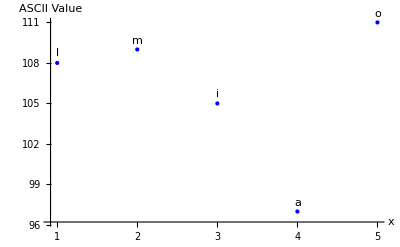

```mathematica
(*Plot original points function*)
points = Transpose[{Range[Length[asciiList]],asciiList}];
charList=Characters[inputString];
labeledPoints=Transpose[{points,charList}];
labeledPointsList=Labeled[#[[1]],#[[2]],Above]&/@labeledPoints;
ListPlot[labeledPointsList,PlotStyle->{PointSize[Medium],Blue},AxesLabel->{"x","ASCII Value"}]
```

126-(167 x)/4+(791 x^2)/24-(41 x^3)/4+(25 x^4)/24

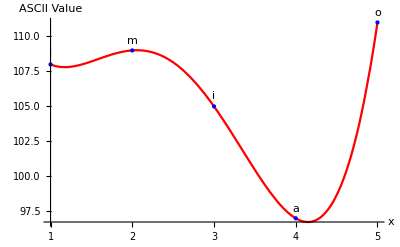

```mathematica
(*Plot polynomial*)
polynomial = Expand[InterpolatingPolynomial[points, x]]
Show[Plot[polynomial,{x,1,Length[asciiList]},PlotStyle->Red,AxesLabel->{"x","ASCII Value"}],ListPlot[labeledPointsList,PlotStyle->{PointSize[Medium], Blue}]]
```

```mathematica
(*Error Retrival points*)
maxErrors = 10;
expandedPoints=Table[{i,polynomial/. x->i},{i,Length[points]+maxErrors}];
asciiListExpanded=Round[Last/@expandedPoints];
stringExpanded = FromCharacterCode[asciiListExpanded]
charListExpanded=FromCharacterCode/@asciiListExpanded;
labeledPointsExpanded=Transpose[{expandedPoints,charListExpanded}];
labeledPointsExpandedList=Labeled[#[[1]],#[[2]],Above]&/@labeledPointsExpanded;
```

lmiaoÆƲΘ۶ౣᒏ⁃ち䗤懠

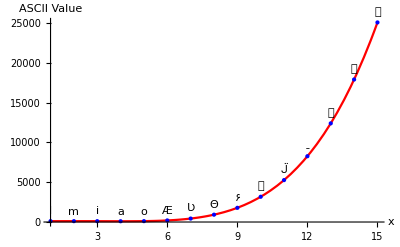

```mathematica
(*Plot polynomial with retriaval error points*)
Show[Plot[polynomial,{x,1,Length[expandedPoints]},PlotStyle->Red,AxesLabel->{"x","ASCII Value"}],ListPlot[labeledPointsExpandedList,PlotStyle->{PointSize[Medium],Blue}]]
```

```mathematica
(* String dirter*)
nErrors = RandomInteger[{1,maxErrors}]
errorsPos= RandomSample[Range[StringLength[stringExpanded]],nErrors]

myStringAsList=Characters[stringExpanded];
myStringAsList=Delete[myStringAsList,List/@errorsPos];
corruptedString=StringJoin[myStringAsList]

strLen = StringLength[stringExpanded]
```

2

{3,8}

lmaoÆƲ۶ౣᒏ⁃ち䗤懠

15

## ...

```mathematica
(*msg_received =  [corruptedString, errorsPos, strLen, maxErrors];*)
```

```mathematica
asciiList =ToCharacterCode[corruptedString]
charList = Characters[corruptedString];
charsPos=Complement[Range[strLen], errorsPos]
points = Transpose[{charsPos,asciiList}]
labeledPoints=Transpose[{points,charList}]
labeledPointsList=Labeled[#[[1]],#[[2]],Above]&/@labeledPoints;
```

{108,109,97,111,198,434,1782,3171,5263,8259,12385,17892,25056}

{1,2,4,5,6,7,9,10,11,12,13,14,15}

{{1,108},{2,109},{4,97},{5,111},{6,198},{7,434},{9,1782},{10,3171},{11,5263},{12,8259},{13,12385},{14,17892},{15,25056}}

{{{1,108},l},{{2,109},m},{{4,97},a},{{5,111},o},{{6,198},Æ},{{7,434},Ʋ},{{9,1782},۶},{{10,3171},ౣ},{{11,5263},ᒏ},{{12,8259},⁃},{{13,12385},ち},{{14,17892},䗤},{{15,25056},懠}}

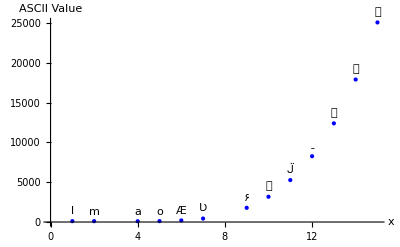

126-(167 x)/4+(791 x^2)/24-(41 x^3)/4+(25 x^4)/24

```mathematica
(*Plot corrupted string points function*)
ListPlot[labeledPointsList,PlotStyle->{PointSize[Medium],Blue},AxesLabel->{"x","ASCII Value"}]
reconstructedPoly = Expand[InterpolatingPolynomial[points,x]]
```

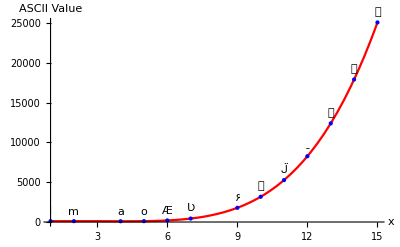

```mathematica
(*Plot polynomial with retriaval error points*)
Show[Plot[reconstructedPoly,{x,1,strLen},PlotStyle->Red,AxesLabel->{"x","ASCII Value"}],ListPlot[labeledPointsList,PlotStyle->{PointSize[Medium],Blue},AxesLabel->{"x","ASCII Value"}]]
```

```mathematica
reconstructedPoints = Table[{i,polynomial/. x->i},{i,strLen-maxErrors}];
reconstructedAsciiList=Round[Last/@reconstructedPoints]
```

{108,109,105,97,111}

```mathematica
reconstructedString = FromCharacterCode[reconstructedAsciiList]
```

lmiao